```mathematica
data  = Import["/Users/philipp/workspace/UNIC/comp-593/m4_data/Monthly-train.csv", "Data"]
```

{1}
 |  |  |  |

```mathematica
Dimensions[data]
```

{48001,2795}

```mathematica
{415,961}
```

{415,961}

```mathematica
Length[data[[2,2;;]]]
```

2794

```mathematica
960
```

960

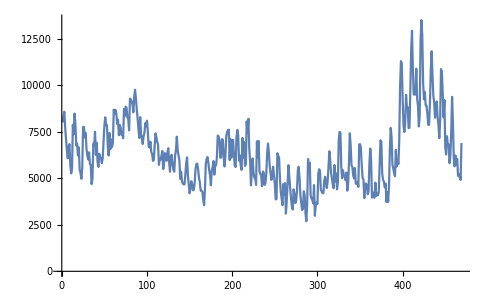

```mathematica
ListLinePlot[data[[2,2;;]]]
```

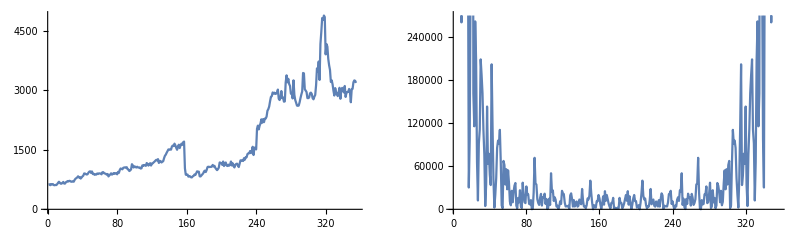

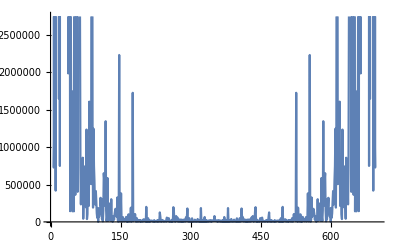

```mathematica
rser = RandomInteger[{2,48001}];
name = data[[rser,1]];
f = DeleteCases[data[[rser,2;;]], ""];
GraphicsRow[{
ListLinePlot[f],
ListLinePlot[Abs[Fourier[f]]^2]}]
```

```mathematica
t = RandomInteger[{2,415}]
```

```mathematica
Head @ t
```

Integer